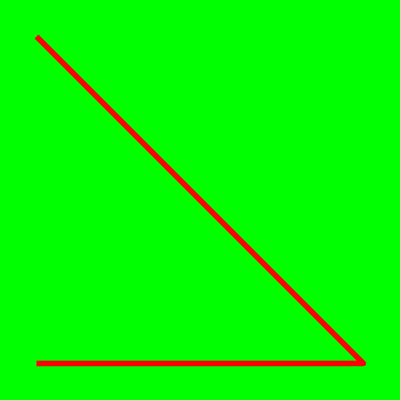

```mathematica
Graphics[{Red,Thickness[0.01],Line[{{0,0},{.5,0},{0,.5}}]},PlotRange->1,Background->Green]
```

```mathematica
{x[1],y[1]}={1,0};alpha[2]=
```

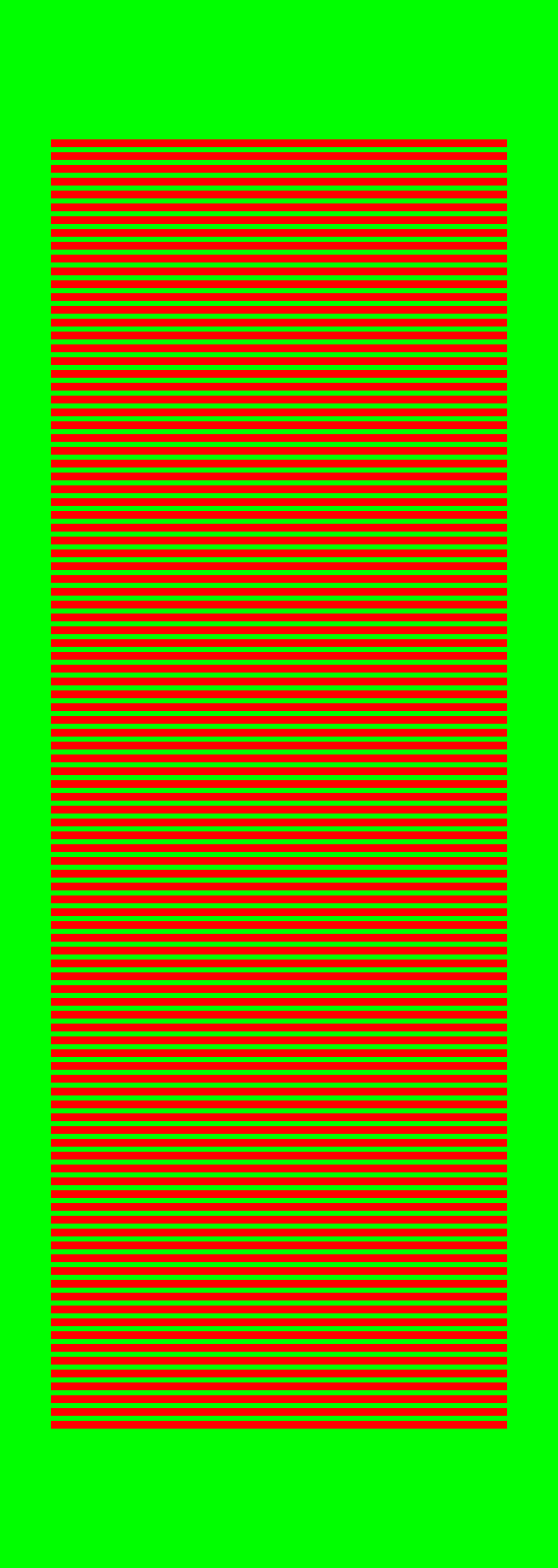

```mathematica
Graphics[{Red,Thickness[0.01],Table[Line[{{0,0+k 0.02},{.5,0+k 0.02}}],{k,-50,50}]},PlotRange->1,Background->Green]
```

```mathematica
101 50
```

5050

```mathematica
Graphics[{ContourPlot[x^10+y^10==1,{x,-1,1},{y,-1,1}],Red,Thickness[0.01],Line[{{0,0},{.5,0},{0,.5}}]},PlotRange->1,Background->Green]
```

-Graphics-

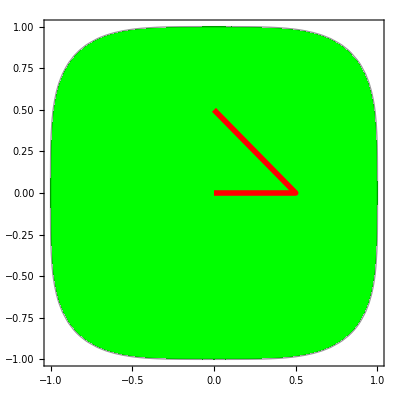

```mathematica
Show[ContourPlot[x^4+y^4,{x,-1,1},{y,-1,1},Contours->1,ColorFunction->(If[#1<1,Green,White]&)],Graphics[{Red,Thickness[0.01],Line[{{0,0},{.5,0},{0,.5}}]}]]
```

```mathematica
Clear[x,y,t,alpha];x[0]=1;y[0]=0;alpha=Random[Real,{0,π},5];coord={};Do[   {alpha=Random[Real,{0,π},5];{x[i],y[i],t[i]}={x[i],y[i],t[i]}/.NSolve[{x[i]^4+y[i]^4==1,x[i]==x[i-1]+0.02 Cos[alpha]t[i],y[i]==y[i-1]+0.02 Sin[alpha]t[i],Abs[t[i]]>10^-12},{x[i],y[i],t[i]},Reals][[1]];AppendTo[coord,{x[i],y[i],t[i]}]}   ,{i,900}]
```

```mathematica
coord
```

{{-0.338415,0.996705,83.4382},{-0.887402,0.785072,-29.4183},{0.767773,-0.898769,-118.056},{-0.999981,-0.0930775,97.1352},{-0.515669,-0.981833,-50.6074},{-0.898815,-0.767699,21.9462},{-0.982038,-0.514247,13.3383},{0.450115,0.989576,103.833},{0.983794,0.501521,-36.1597},{-0.991213,0.43156,-98.8123}}

```mathematica
{#[[1]],#[[2]]}&/@coord
```

{{-0.338415,0.996705},{-0.887402,0.785072},{0.767773,-0.898769},{-0.999981,-0.0930775},{-0.515669,-0.981833},{-0.898815,-0.767699},{-0.982038,-0.514247},{0.450115,0.989576},{0.983794,0.501521},{-0.991213,0.43156}}

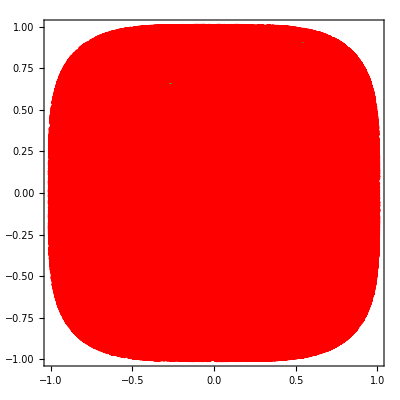

```mathematica
Show[ContourPlot[x^4+y^4,{x,-1,1},{y,-1,1},Contours->1,ColorFunction->(If[#1<1,Green,White]&)],Graphics[{Red,Thickness[0.01],Line[Prepend[{#[[1]],#[[2]]}&/@coord,{1,0}]]}]]
```

```mathematica
Total[Abs[#[[3]]&/@coord]]
```

60790.5

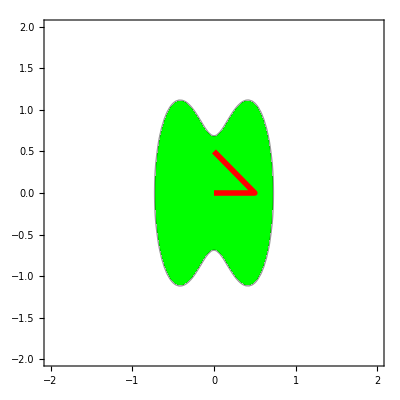

```mathematica
Show[ContourPlot[((4x-2)^2+y^2)((4x+2)^2+y^2)-19,{x,-2,2},{y,-2,2},Contours->{1},ColorFunction->(If[#1<1,Green,White]&)],Graphics[{Red,Thickness[0.01],Line[{{0,0},{.5,0},{0,.5}}]}]]
```

```mathematica
Clear[x,y,t,alpha];x[0]=√((4+√20)/16);y[0]=0;alpha=Random[Real,{0,π},5];coord={};Do[   {alpha=Random[Real,{0,π},5];{x[i],y[i],t[i]}={x[i],y[i],t[i]}/.NSolve[{((4x[i]-2)^2+y[i]^2)((4x[i]+2)^2+y[i]^2)==20,x[i]==x[i-1]+0.02 Cos[alpha]t[i],y[i]==y[i-1]+0.02 Sin[alpha]t[i],Abs[t[i]]>10^-12},{x[i],y[i],t[i]},Reals][[1]];AppendTo[coord,{x[i],y[i],t[i]}]}   ,{i,100}]
```

```mathematica
x[0]//N
```

0.727673

```mathematica
coord
```

{{0.236765,0.981851,54.8867},{0.440666,-1.11462,-105.318},{0.0227472,0.69184,92.7085},{-0.6702,-0.65704,-75.823},{-0.430337,1.1168,89.4991},{-0.355416,1.10153,-3.82298},{0.701241,-0.458773,-94.2216},{-0.311876,1.06981,91.6921},{-0.620225,0.854334,-18.8089},{-0.20571,0.935782,21.122},{-0.673108,0.641996,-27.603},{-0.463399,1.10584,25.4524},{0.665316,-0.681163,-105.681},{0.437217,-1.11547,-24.528},{0.618257,-0.860341,15.6417},{0.618257,-0.860341,-1.27645×10^-11},{0.721438,0.226914,54.607},{0.717873,0.283583,2.83905},{-0.694625,0.509865,71.5254},{-0.458662,1.10813,32.156},{-0.0244259,-0.692556,-92.6153},{0.712572,0.350351,63.8518},{0.178767,0.892899,38.0561},{-0.727672,0.00386734,-63.4824},{0.649158,-0.752266,-78.5398},{0.300241,1.05877,92.2171},{0.661885,-0.697316,-89.6469},{0.138166,0.82659,80.5694},{0.712687,0.349052,-37.3536},{0.5352,1.03809,35.5766},{0.235777,-0.980457,-102.032},{0.606417,-0.894344,19.0256},{0.358386,-1.10312,-16.21},{0.626169,-0.835538,18.9279},{0.224492,-0.964178,-21.0887},{0.649714,-0.750016,23.8054},{-0.661722,0.698065,97.6832},{-0.206208,0.936553,25.7084},{0.494313,-1.08458,-106.954},{0.301034,1.05956,107.641},{0.638118,0.794525,-21.4399},{-0.727663,0.0092851,-78.7712},{0.713668,-0.337727,-74.1258},{0.285099,-1.04289,-41.2591},{-0.449364,-1.11192,-36.885},{-0.490197,1.08806,110.018},{-0.692592,0.524321,-29.9486},{-0.275642,-1.03214,-80.5669},{-0.066061,0.724928,88.476},{-0.502811,1.07672,28.0406},{-0.394678,1.11611,5.75423},{-0.545511,1.02268,-8.87131},{-0.629579,0.824291,-10.7734},{0.571504,-0.976332,-108.222},{0.528034,1.04788,101.234},{0.414287,1.11803,6.68196},{0.494178,-1.0847,-110.209},{0.178671,0.892744,100.123},{-0.422875,1.11769,32.1115},{-0.284338,1.04205,-7.89224},{0.676297,-0.624856,-96.1948},{-0.474438,1.09952,103.654},{-0.416699,1.11801,3.03132},{-0.633731,0.810114,-18.835},{-0.201563,0.929321,22.4154},{-0.688336,-0.553017,-78.0108},{0.724384,0.165248,79.2415},{0.193266,-0.916226,-60.2427},{0.723189,0.192737,61.4536},{0.234727,0.978969,46.2806},{-0.441578,-1.11437,-109.994},{-0.260372,-1.0135,10.3694},{-0.686997,-0.561648,31.0718},{0.657604,0.71663,92.7624},{-0.725525,0.133686,-75.0478},{-0.187503,0.907014,47.1037},{-0.65691,0.71968,-25.2704},{-0.471971,1.10105,21.1925},{-0.102984,0.77223,-24.7122},{-0.655408,0.726201,-27.7169},{-0.701219,-0.458948,-59.3017},{-0.421508,-1.1178,-35.7882},{-0.117735,-0.794292,22.1886},{-0.70962,-0.382052,36.0649},{0.694311,-0.512136,-70.4972},{-0.642607,0.777888,92.8912},{-0.354587,1.10108,21.6453},{-0.359551,1.10372,0.281121},{-0.430008,1.11685,3.58352},{0.481041,-1.09508,-119.61},{0.221447,0.959679,103.555},{-0.661693,0.698203,-46.0517},{-0.176406,0.889061,26.0735},{-0.674619,0.63396,-27.9863},{-0.399385,-1.11691,-88.6186},{0.230526,0.972963,109.137},{-0.634416,0.807722,-44.0292},{-0.72611,-0.114105,-46.3188},{0.611943,-0.878916,-77.0604},{0.0301903,0.695388,83.9177}}

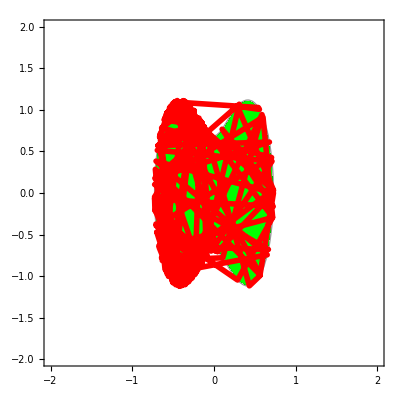

```mathematica
Show[ContourPlot[((4x-2)^2+y^2)((4x+2)^2+y^2)-19,{x,-2,2},{y,-2,2},Contours->{1},ColorFunction->(If[#1<1,Green,White]&)],Graphics[{Red,Thickness[0.01],Line[Prepend[{#[[1]],#[[2]]}&/@coord,{x[0],0}]]}]]
```

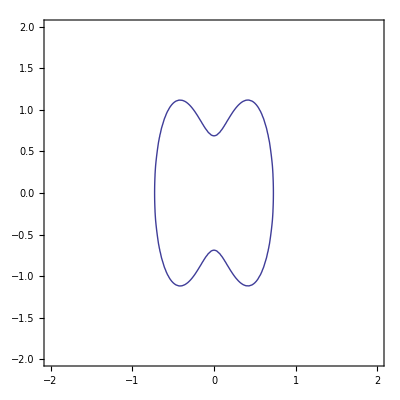

```mathematica
ContourPlot[((4x-2)^2+y^2)((4x+2)^2+y^2)==20,{x,-2,2},{y,-2,2}]
```

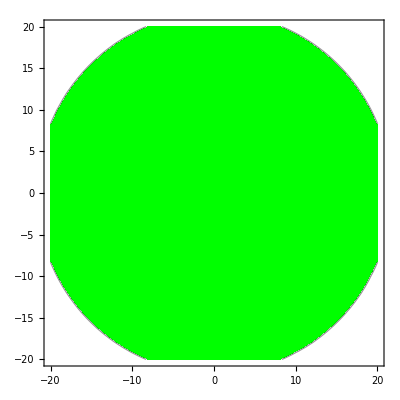

```mathematica
Show[ContourPlot[((x-1/4)^2+y^2)((x+1/4)^2+y^2),{x,-20,20},{y,-20,20},Contours->1,ColorFunction->(If[#1<1,Green,White]&)]]
```

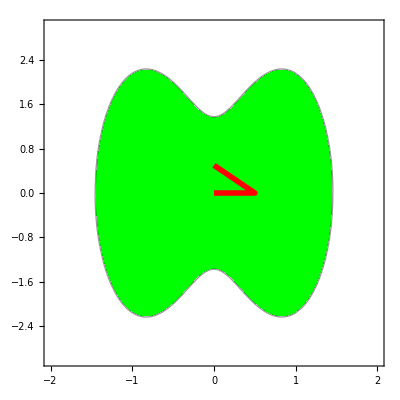

```mathematica
Show[ContourPlot[((2x-2)^2+y^2/4)((2x+2)^2+y^2/4)-19,{x,-2,2},{y,-3,3},Contours->{1},ColorFunction->(If[#1<1,Green,White]&)],Graphics[{Red,Thickness[0.01],Line[{{0,0},{.5,0},{0,.5}}]}]]
```

```mathematica
Clear[x,y,t,alpha];x[0]=2 √((4+√20)/16);y[0]=0;alpha=Random[Real,{0,π},5];coord={};Do[   {alpha=Random[Real,{0,π},5];{x[i],y[i],t[i]}={x[i],y[i],t[i]}/.NSolve[{((2x[i]-2)^2+y[i]^2/4)((2x[i]+2)^2+y[i]^2/4)==20,x[i]==x[i-1]+0.02 Cos[alpha]t[i],y[i]==y[i-1]+0.02 Sin[alpha]t[i],Abs[t[i]]>10^-12},{x[i],y[i],t[i]},Reals][[1]];AppendTo[coord,{x[i],y[i],t[i]}]}   ,{i,100}]
```

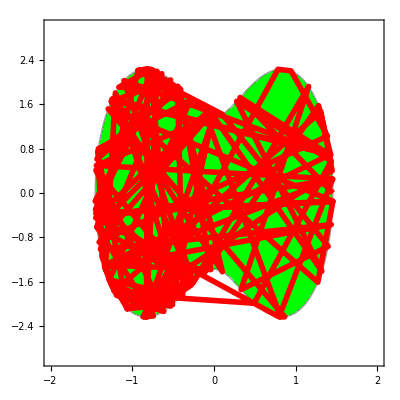

```mathematica
Show[ContourPlot[((2x-2)^2+y^2/4)((2x+2)^2+y^2/4)-19,{x,-2,2},{y,-3,3},Contours->{1},ColorFunction->(If[#1<1,Green,White]&)],Graphics[{Red,Thickness[0.01],Line[Prepend[{#[[1]],#[[2]]}&/@coord,{x[0],0}]]}]]
```

```mathematica
x[0]//N
```

0.727673

```mathematica
Clear[x,y,t,alpha];x[0]=1/2;y[0]=-2;alpha=Random[Real,{0,π},5];coord={};Do[   {alpha=2.3571;{x[i],y[i],t[i]}={x[i],y[i],t[i]}/.NSolve[{((2x[i]-2)^2+y[i]^2/4)((2x[i]+2)^2+y[i]^2/4)==20,x[i]==x[i-1]+0.02 Cos[alpha]t[i],y[i]==y[i-1]+0.02 Sin[alpha]t[i],Abs[t[i]]>10^-12},{x[i],y[i],t[i]},Reals][[1]];AppendTo[coord,{x[i],y[i],t[i]}]}   ,{i,1}]
```

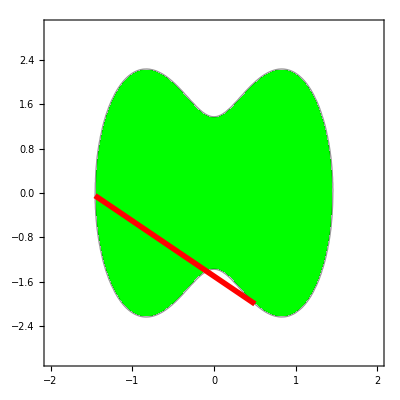

```mathematica
Show[ContourPlot[((2x-2)^2+y^2/4)((2x+2)^2+y^2/4)-19,{x,-2,2},{y,-3,3},Contours->{1},ColorFunction->(If[#1<1,Green,White]&)],Graphics[{Red,Thickness[0.01],Line[Prepend[{#[[1]],#[[2]]}&/@coord,{x[0],y[0]}]]}]]
```

```mathematica
alpha
```

2.3571

```mathematica
x[0]
```

x[0]

```mathematica
Clear[x,y,t];i=1;x[0]=1/2;y[0]=-2;NSolve[{((2x-2)^2+y^2/4)((2x+2)^2+y^2/4)==20,x==x[0]+0.02 Cos[alpha]t,y==y[0]+0.02 Sin[alpha]t,Abs[t]>10^-12,((2x-2)^2+y^2/4)((2x+2)^2+y^2/4)-19},{x,y,t},Reals]
```

{{x→-1.45521,y→-0.0483309,t→138.129},{x→-0.0903611,y→-1.41071,t→41.7071},{x→0.692978,y→-2.19263,t→-13.6333}}